## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: DoublePendulumStiff.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/61-Newton Sinplifikatua/61-B (Artikulurako inplementazioa 17-03-2017)/Packages/

```mathematica
Get["DoublePendulumStiffNEW`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Black;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleHairer=Green;
StyleError=Black;
StyleEstimation=Lighter[Blue,.6];
StyleHamT12=Directive[Dashed,Red];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

### Paths

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

### Input Files

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileB=NotebookDirectory[]<>DataDirectory<>"outB.bin";
fileC=NotebookDirectory[]<> DataDirectory<>"outC.bin";
fileD=NotebookDirectory[]<>DataDirectory<>"outD.bin"; 
fileE=NotebookDirectory[]<>DataDirectory<>"outE.bin"; 
fileF=NotebookDirectory[]<>DataDirectory<>"outF.bin"; 
fileG=NotebookDirectory[]<>DataDirectory<>"outG.bin"; 
fileH=NotebookDirectory[]<>DataDirectory<>"outH.bin"; 
fileI=NotebookDirectory[]<>DataDirectory<>"outI.bin"; 
fileJ=NotebookDirectory[]<>DataDirectory<>"outJ.bin"; 
fileK=NotebookDirectory[]<>DataDirectory<>"outK.bin"; 
fileL=NotebookDirectory[]<>DataDirectory<>"outL.bin";
```

### Output Files

```mathematica
esperiment="NCDP";
plot1=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot1b.pdf";
plot2=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot2.pdf";
plot11=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot11.pdf";
plot12=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot12.pdf";
plot13=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot13.pdf";
plot3=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot3b.pdf";
plot4=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot4.pdf";
plot5=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot5.pdf";
plot5D=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot5D.pdf";
plot6=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot6.pdf";
plot6a=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot6a.pdf";
plot7=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot7.pdf";
```

## Parameters (NCDP-STIFF initial values)

### Problem parameters and initial values.

```mathematica
prec=100;
n=2;
neq=4;
g=98/10;
m1=1;m2=1;
l1=1;l2=1;
k=1;
```

```mathematica
CC=Join[{0},Map[2^# &, Range[11]]];
CC8=1/2 CC^2
KK=CC^2
```

{0,2,8,32,128,512,2048,8192,32768,131072,524288,2097152}

{0,4,16,64,256,1024,4096,16384,65536,262144,1048576,4194304}

```mathematica
C1=-l1^2 (m1+m2);
C2=-l2^2 m2;
C3=-2 l1 l2 m2 ;
C4=-2 l1^2 l2^2 m1 m2-l1^2 l2^2 m2^2;
C5=-l1^2 l2^2 m2^2;
C6=g l1 (m1+m2);
C7= g l2 m2;
C8=k/2;

Q10=(11/10);Q20=-(11/10);
P10=13873/5000;
P20=13873/5000;
u0={Q10,Q20,P10,P20};
u0D= N[{Q10,Q20,P10,P20}];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;

Q20A=Q20/Sqrt[1+100KK[[1]]];
Q20B=Q20/Sqrt[1+100KK[[2]]];
Q20C=Q20/Sqrt[1+100KK[[3]]];
Q20D=Q20/Sqrt[1+100KK[[4]]];
Q20E=Q20/Sqrt[1+100KK[[5]]];
Q20F=Q20/Sqrt[1+100KK[[6]]];
Q20G=Q20/Sqrt[1+100KK[[7]]];
Q20H=Q20/Sqrt[1+100KK[[8]]];
Q20I=Q20/Sqrt[1+100KK[[9]]];
Q20J=Q20/Sqrt[1+100KK[[10]]];
Q20K=Q20/Sqrt[1+100KK[[11]]];
Q20L=Q20/Sqrt[1+100KK[[12]]];

uu0A={Q10,Q20A,P10,P20};
uu0B={Q10,Q20B,P10,P20};
uu0C={Q10,Q20C,P10,P20};
uu0D={Q10,Q20D,P10,P20};
uu0E={Q10,Q20E,P10,P20};
uu0F={Q10,Q20F,P10,P20};
uu0G={Q10,Q20G,P10,P20};
uu0H={Q10,Q20H,P10,P20};
uu0I={Q10,Q20I,P10,P20};
uu0J={Q10,Q20J,P10,P20};
uu0K={Q10,Q20K,P10,P20};
uu0L={Q10,Q20L,P10,P20};

uu0AD= N[uu0A];
uu0BD= N[uu0B];
uu0CD= N[uu0C];
uu0DD= N[uu0D];
uu0ED= N[uu0E];
uu0FD= N[uu0F];
uu0GD= N[uu0G];
uu0HD= N[uu0H];
uu0ID= N[uu0I];
uu0JD= N[uu0J];
uu0KD= N[uu0K];
uu0LD= N[uu0L];

uu0ADD=SetPrecision[uu0AD,prec];
uu0BDD=SetPrecision[uu0BD,prec];
uu0CDD=SetPrecision[uu0CD,prec];
uu0DDD=SetPrecision[uu0DD,prec];
uu0EDD=SetPrecision[uu0ED,prec];
uu0FDD=SetPrecision[uu0FD,prec];
uu0GDD=SetPrecision[uu0GD,prec];
uu0HDD=SetPrecision[uu0HD,prec];
uu0IDD=SetPrecision[uu0ID,prec];
uu0JDD=SetPrecision[uu0JD,prec];
uu0KDD=SetPrecision[uu0KD,prec];
uu0LDD=SetPrecision[uu0LD,prec];

ee0A =uu0A -uu0ADD;
ee0B =uu0B - uu0BDD;
ee0C =uu0C - uu0CDD;
ee0D =uu0D - uu0DDD;
ee0E =uu0E - uu0EDD;
ee0F =uu0F - uu0FDD;
ee0G =uu0G - uu0GDD;
ee0H =uu0H - uu0HDD;
ee0I =uu0I - uu0IDD;
ee0J =uu0J - uu0JDD;
ee0K =uu0K - uu0KDD;
ee0L =uu0L - uu0LDD;

preal=parameters={C1,C2,C3,C4,C5,C6,C7,C8};
prealA={C1,C2,C3,C4,C5,C6,C7,KK[[1]]/2};
prealB={C1,C2,C3,C4,C5,C6,C7,KK[[2]]/2};
prealC={C1,C2,C3,C4,C5,C6,C7,KK[[3]]/2};
prealD={C1,C2,C3,C4,C5,C6,C7,KK[[4]]/2};
prealE={C1,C2,C3,C4,C5,C6,C7,KK[[5]]/2};
prealF={C1,C2,C3,C4,C5,C6,C7,KK[[6]]/2};
prealG={C1,C2,C3,C4,C5,C6,C7,KK[[7]]/2};
prealH={C1,C2,C3,C4,C5,C6,C7,KK[[8]]/2};
prealI={C1,C2,C3,C4,C5,C6,C7,KK[[9]]/2};
prealJ={C1,C2,C3,C4,C5,C6,C7,KK[[10]]/2};
prealK={C1,C2,C3,C4,C5,C6,C7,KK[[11]]/2};
prealL={C1,C2,C3,C4,C5,C6,C7,KK[[12]]/2};
pint={0,0};
```

```mathematica
u0
```

{11/10,-11/10,13873/5000,13873/5000}

```mathematica
parameters
```

{-2,-1,-2,-3,-1,98/5,49/5,1/2}

### Integration parameters.

```mathematica
t0=0.;tend=2.^(12) ;
h=2.^(-7);
sampling=2^(10);
```

```mathematica
codfun0=1; (*OdePendulumSTIFF*)

ns= 6;
nstep=(tend-t0)/h;
nout=nstep/sampling
```

512.

### RKG parameters

```mathematica
neq=Length[u0];
prec=100;
HAM=DoublePendulumSTIFFHamNEW;
HAM2=DoublePendulumSTIFFHam3NEW;
ERR=ErrorPosition;
```

## Import (mathematica execution)

```mathematica
Now
```

Mon 20 Mar 2017 17:50:46GMT+1.

```mathematica
nstat=1;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
noutB=noutC=noutD=noutA;
noutE=noutF=noutG=noutH=noutI=noutJ=noutK=noutL=noutA;

step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real64"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
{Length[outA],Length[outA[[1]]]}
```

{1,513}

```mathematica
outB=SetPrecision[ArrayReshape[BinaryReadList[fileB,"Real64"],{nstat,noutB,dd1}],prec];
tpB=Flatten[Take[outB[[1]],All,{1,1}]];
tpB=Map[First,Partition[tpB,step]];
{Length[outB],Length[outB[[1]]]}
```

{1,513}

```mathematica
outC=SetPrecision[ArrayReshape[BinaryReadList[fileC,"Real64"],{nstat,noutC,dd1}],prec];
tpC=Flatten[Take[outC[[1]],All,{1,1}]];
tpC=Map[First,Partition[tpC,step]];
{Length[outC],Length[outC[[1]]]}
```

{1,513}

```mathematica
outD=SetPrecision[ArrayReshape[BinaryReadList[fileD,"Real64"],{nstat,noutD,dd1}],prec];
tpD=Flatten[Take[outD[[1]],All,{1,1}]];
tpD=Map[First,Partition[tpD,step]];
{Length[outD],Length[outD[[1]]]}
```

{1,513}

```mathematica
outE=SetPrecision[ArrayReshape[BinaryReadList[fileE,"Real64"],{nstat,noutE,dd1}],prec];
tpE=Flatten[Take[outE[[1]],All,{1,1}]];
tpE=Map[First,Partition[tpE,step]];
{Length[outE],Length[outE[[1]]]}
```

{1,513}

```mathematica
outF=SetPrecision[ArrayReshape[BinaryReadList[fileF,"Real64"],{nstat,noutF,dd1}],prec];
tpF=Flatten[Take[outF[[1]],All,{1,1}]];
tpF=Map[First,Partition[tpF,step]];
{Length[outF],Length[outF[[1]]]}
```

{1,513}

```mathematica
outG=SetPrecision[ArrayReshape[BinaryReadList[fileG,"Real64"],{nstat,noutG,dd1}],prec];
tpG=Flatten[Take[outG[[1]],All,{1,1}]];
tpG=Map[First,Partition[tpG,step]];
{Length[outG],Length[outG[[1]]]}
```

{1,513}

```mathematica
outH=SetPrecision[ArrayReshape[BinaryReadList[fileH,"Real64"],{nstat,noutH,dd1}],prec];
tpH=Flatten[Take[outH[[1]],All,{1,1}]];
tpH=Map[First,Partition[tpH,step]];
{Length[outH],Length[outH[[1]]]}
```

{1,513}

```mathematica
outI=SetPrecision[ArrayReshape[BinaryReadList[fileI,"Real64"],{nstat,noutI,dd1}],prec];
tpI=Flatten[Take[outI[[1]],All,{1,1}]];
tpI=Map[First,Partition[tpI,step]];
{Length[outI],Length[outI[[1]]]}
```

{1,513}

```mathematica
outJ=SetPrecision[ArrayReshape[BinaryReadList[fileJ,"Real64"],{nstat,noutJ,dd1}],prec];
tpJ=Flatten[Take[outJ[[1]],All,{1,1}]];
tpJ=Map[First,Partition[tpJ,step]];
{Length[outJ],Length[outJ[[1]]]}
```

{1,513}

```mathematica
outK=SetPrecision[ArrayReshape[BinaryReadList[fileK,"Real64"],{nstat,noutK,dd1}],prec];
tpK=Flatten[Take[outK[[1]],All,{1,1}]];
tpK=Map[First,Partition[tpK,step]];
{Length[outK],Length[outK[[1]]]}
```

{1,513}

```mathematica
outL=SetPrecision[ArrayReshape[BinaryReadList[fileL,"Real64"],{nstat,noutL,dd1}],prec];
tpL=Flatten[Take[outL[[1]],All,{1,1}]];
tpL=Map[First,Partition[tpL,step]];
{Length[outL],Length[outL[[1]]]}
```

{1,513}

## Analisis-I

### Graphics-I (Energy): Plot1, Plot2

```mathematica
{MeanHamA,DesvHamA}=FunEnergy[outA, nstat,noutA,HAM, prealA,neq,prec,step] ;
{MeanHamB,DesvHamB}=FunEnergy [outB, nstat,noutB,HAM,prealB,neq,prec,step] ;
{MeanHamC,DesvHamC}=FunEnergy[outC, nstat,noutC,HAM, prealC,neq,prec,step] ;
{MeanHamD,DesvHamD}=FunEnergy[outD, nstat,noutD,HAM, prealD,neq,prec,step] ;
{MeanHamE,DesvHamE}=FunEnergy[outE, nstat,noutE,HAM, prealE,neq,prec,step] ;
{MeanHamF,DesvHamF}=FunEnergy[outF, nstat,noutF,HAM, prealF,neq,prec,step] ;
{MeanHamG,DesvHamG}=FunEnergy[outG, nstat,noutG,HAM, prealG,neq,prec,step] ;
{MeanHamH,DesvHamH}=FunEnergy[outH, nstat,noutH,HAM, prealH,neq,prec,step] ;
{MeanHamI,DesvHamI}=FunEnergy[outI, nstat,noutI,HAM, prealI,neq,prec,step] ;
{MeanHamJ,DesvHamJ}=FunEnergy[outJ, nstat,noutJ,HAM, prealJ,neq,prec,step] ;
{MeanHamK,DesvHamK}=FunEnergy[outK, nstat,noutK,HAM, prealK,neq,prec,step] ;
{MeanHamL,DesvHamL}=FunEnergy[outL, nstat,noutL,HAM, prealL,neq,prec,step] ;
```

#### Plot (1)

```mathematica
eskala=10^(15);
eskala=1;
```

```mathematica
MeanHamAdata = Transpose[{tpA,Log10[Abs[MeanHamA]]}];
MeanHamBdata = Transpose[{tpB,Log10[Abs[MeanHamB]]}];
MeanHamCdata = Transpose[{tpC,Log10[Abs[MeanHamC]]}];
MeanHamDdata = Transpose[{tpD,Log10[Abs[MeanHamD]]}];
MeanHamEdata = Transpose[{tpE,Log10[Abs[MeanHamE]]}];
MeanHamFdata = Transpose[{tpF,Log10[Abs[MeanHamF]]}];
MeanHamGdata = Transpose[{tpG,Log10[Abs[MeanHamG]]}];
MeanHamHdata = Transpose[{tpH,Log10[Abs[MeanHamH]]}];
MeanHamIdata = Transpose[{tpI,Log10[Abs[MeanHamI]]}];
MeanHamJdata = Transpose[{tpJ,Log10[Abs[MeanHamJ]]}];
MeanHamKdata = Transpose[{tpK,Log10[Abs[MeanHamK]]}];
MeanHamLdata = Transpose[{tpL,Log10[Abs[MeanHamL]]}];

DesvHamAdata = Transpose[{tpA,DesvHamA*eskala}];
DesvHamBdata = Transpose[{tpB,DesvHamB*eskala}];
DesvHamCdata = Transpose[{tpC,DesvHamC*eskala}];
DesvHamDdata = Transpose[{tpD,DesvHamD*eskala}];
DesvHamEdata = Transpose[{tpE,DesvHamE*eskala}];
```

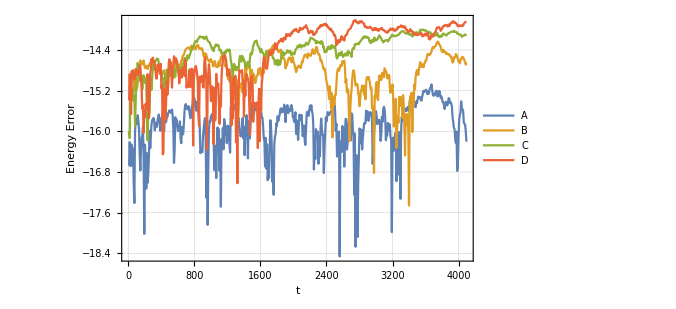

```mathematica
plot=ListPlot[{MeanHamAdata,MeanHamBdata,MeanHamCdata,MeanHamDdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
(*PlotRange->{{x0,x1},{y0,y1}},*)
PlotLegends->Placed[{"A","B","C","D"(*,"standard deviation"*)},Below],
(*PlotLabels->Placed[{"ΔE","ΔE","ΔE","σ","σ","σ"},{Scaled[1],Above}],*)
PlotTheme->"Detailed",
ImageSize->500,
(*PlotStyle->{StyleIdeal,StyleMachine,StyleHairer,StyleIdeal,StyleMachine,StyleHairer},*)
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy Error"},
LabelStyle->Directive[Black,Bold]
]
```

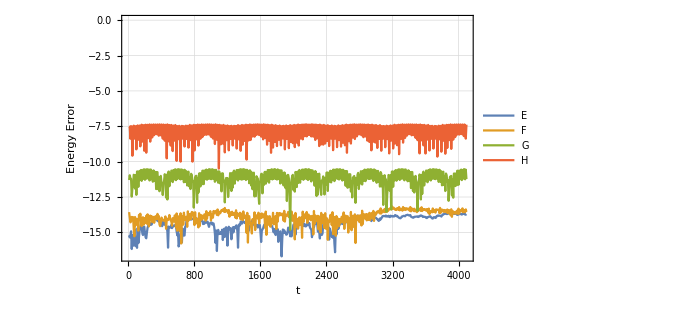

```mathematica
plot=ListPlot[{MeanHamEdata,MeanHamFdata,MeanHamGdata,MeanHamHdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
(*PlotRange->{{x0,x1},{y0,y1}},*)
PlotLegends->Placed[{"E","F","G","H"(*,"standard deviation"*)},Below],
(*PlotLabels->Placed[{"ΔE","ΔE","ΔE","σ","σ","σ"},{Scaled[1],Above}],*)
PlotTheme->"Detailed",
ImageSize->500,
(*PlotStyle->{StyleIdeal,StyleMachine,StyleHairer,StyleIdeal,StyleMachine,StyleHairer},*)
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy Error"},
LabelStyle->Directive[Black,Bold]
]
```

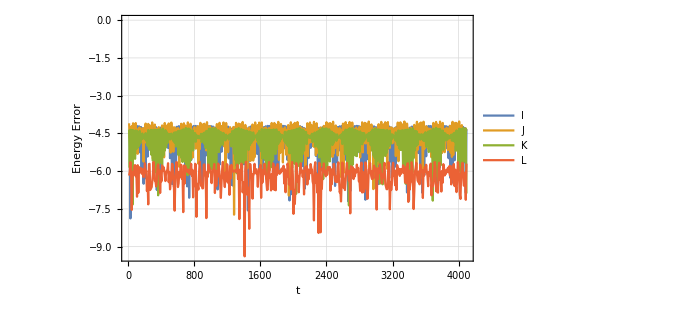

```mathematica
plot=ListPlot[{MeanHamIdata,MeanHamJdata,MeanHamKdata,MeanHamLdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
(*PlotRange->{{x0,x1},{y0,y1}},*)
PlotLegends->Placed[{"I","J","K","L"(*,"standard deviation"*)},Below],
(*PlotLabels->Placed[{"ΔE","ΔE","ΔE","σ","σ","σ"},{Scaled[1],Above}],*)
PlotTheme->"Detailed",
ImageSize->500,
(*PlotStyle->{StyleIdeal,StyleMachine,StyleHairer,StyleIdeal,StyleMachine,StyleHairer},*)
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy Error"},
LabelStyle->Directive[Black,Bold]
]
```